```mathematica
path=NotebookDirectory[];
```

## Study saturated doublebang protocol for LMG

### Doesn’t change much changing the number of spins

{/home/lk/Documents/docs/research/Ricardo/quantum-control-critical-point/results/rabi_and_lmg_optimizations_20190228/lmg_doublebang_powell.csv,/home/lk/Documents/docs/research/Ricardo/quantum-control-critical-point/results/lmg_different_spinnumbers_20190228/lmg_doublebang_powell_100spins.csv,/home/lk/Documents/docs/research/Ricardo/quantum-control-critical-point/results/lmg_different_spinnumbers_20190228/lmg_doublebang_powell_150spins.csv}

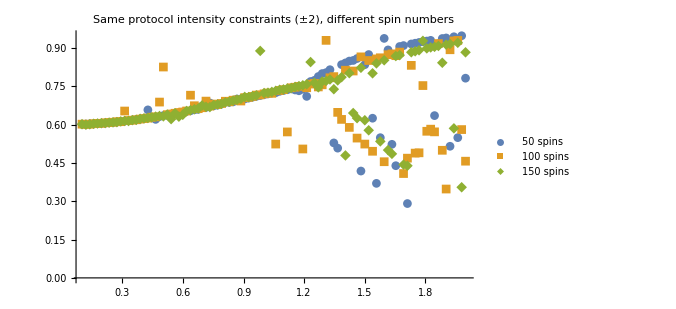

```mathematica
With[{data=Import[#]⟦2;;,2;;⟧&/@Echo@Prepend[
FileNames@FileNameJoin@{path,"lmg_different_spinnumbers_20190228","lmg_doublebang_powell*.csv"},
First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_20190228","lmg_doublebang_powell*.csv"}
]},
With[{points=Map[{#⟦1⟧,#⟦4⟧/#⟦1⟧}&,data,{2}]},
ListPlot[points,
PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"50 spins","100 spins","150 spins"},ImageSize->500,PlotLabel->"Same protocol intensity constraints (±2), different spin numbers"
]
]
]
```

```mathematica
With[{data=Import[#]⟦2;;,2;;⟧&/@Echo@Prepend[
FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_different_constraints_20190228","lmg_doublebang_powell*.csv"},
First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_20190228","lmg_doublebang_powell*.csv"}
]},
With[{points=Map[{#⟦1⟧,#⟦4⟧/#⟦1⟧,#⟦3⟧/#⟦5⟧}&,data,{2}]},
Echo@Dimensions@points;
Graphics3D[{
Table[{Hue[k/3],Point@points⟦k⟧},{k,3}],
Opacity@0.4,InfinitePlane[{0,0,-1},{{1,0,0},{0,1,0}}]
},
Axes->True,AxesLabel->{"tf","t1/tf","y0/y1"},BoxRatios->1,
PlotRange->{All,All,{-40,40}},ImageSize->500,PlotLabel->"50 spins, different max protocol intensities"
]
]
]
```

{/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_20190228/lmg_doublebang_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds3.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds5.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds7.csv}

{4,100,3}

-Graphics3D-

{/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_20190228/lmg_doublebang_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds3.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds5.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds7.csv}

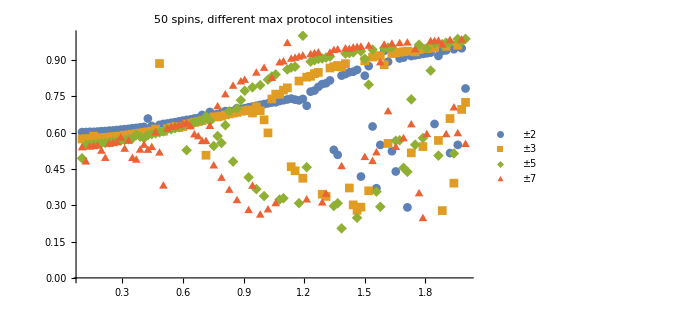

```mathematica
With[{data=Import[#]⟦2;;,2;;⟧&/@Echo@Prepend[
FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_different_constraints_20190228","lmg_doublebang_powell*.csv"},
First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_20190228","lmg_doublebang_powell*.csv"}
]},
With[{points=Map[{#⟦1⟧,#⟦4⟧/#⟦1⟧}&,data,{2}]},
ListPlot[points,
PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"±2","±3","±5","±7"},ImageSize->500,PlotLabel->"50 spins, different max protocol intensities"
]
]
]
```

### Scans of all combinations of total time and t_1/t_f ratio for LMG

Use this to plot a ContourPlot for a single scan

```mathematica
With[{data=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*.csv"}}},
ListContourPlot[
data⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->Append[Range[0,1,0.05],0.99],
FrameLabel->{"tf","t1/tf"},PlotRangePadding->None,PerformanceGoal->"Quality"
]]
```

Plot a row of contour plots for several scans (same spin, different constraints)

```mathematica
fig=With[{datafiles=#⟦;;-4⟧&@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import/@datafiles//Map[#⟦2;;,2;;⟧&]},
dataSets//Map[MinMax@#⟦All,3⟧&]
]]
```

{{0.184365,0.998875},{0.0297422,0.998398},{0.00598239,0.998286},{0.00498634,0.997331},{0.000438177,0.996625},{0.0000730586,0.994858}}

```mathematica
protectFromLineExportLineBreaks[fig_]:=Cell[BoxData@ToBoxes@fig,PageWidth->Infinity]
```

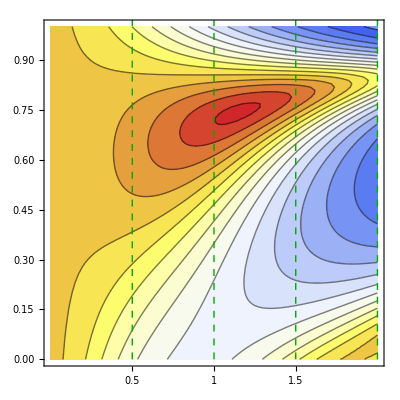
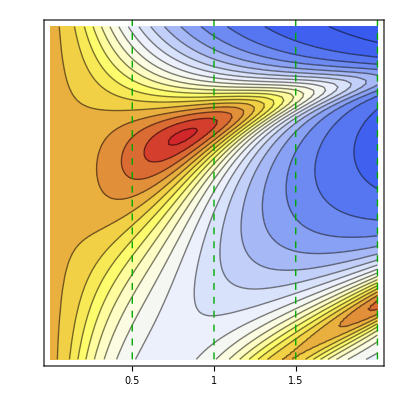
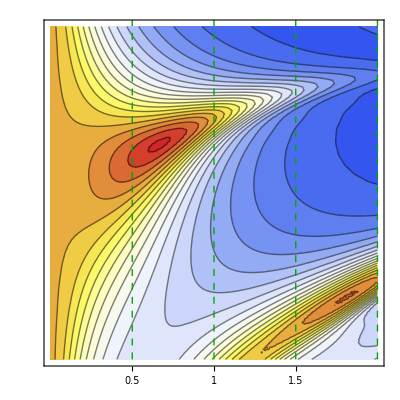
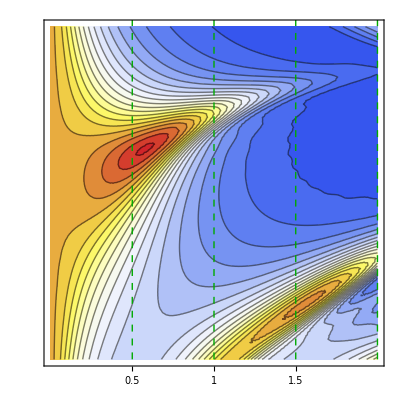
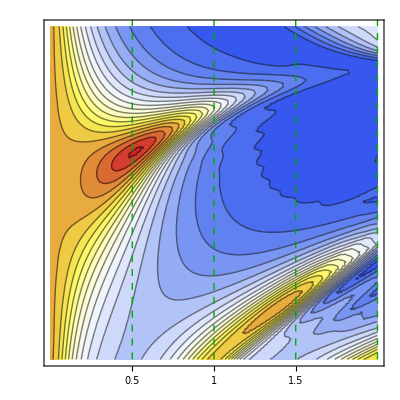
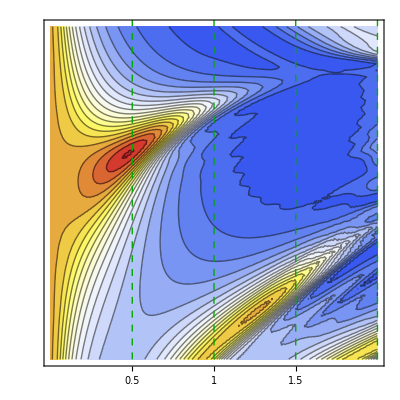

```mathematica
fig=With[{datafiles=#⟦;;-4⟧&@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import/@datafiles},
Row[Table[
ListContourPlot[
dataSets⟦idx⟧⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",Contours->Append[Range[0,1,0.05],0.99],
PlotRangePadding->0,
ImagePadding->If[idx==1,{{60,4},{60,0}},{{0,4},{60,0}}],
ImageMargins->None,
FrameTicks->If[idx==1,{{Automatic,None},{{0.5,1,1.5},None}},{{None,None},{{0.5,1,1.5},None}}],
Frame->True,FrameStyle->Directive[Black,Thickness@0.01],
FrameLabel->{MaTeX["\\omega\\tau",Magnification->1.8],MaTeX["\\tau_1/\\tau",Magnification->1.8]},
ImageSize->{Automatic,280},
LabelStyle->Directive[Black,FontFamily->"DejaVu Sans",FontSize->18],
Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.5,1,1.5,2}}]},
PlotLabel->MaTeX["g_{\\operatorname{max}}="<>ToString@ToExpression@StringTake[FileBaseName@datafiles⟦idx⟧,-2],Magnification->1.8]
],
{idx,Length@dataSets}
]~Append~BarLegend["TemperatureMap",Append[Range[0,0.9,0.1],0.99],LabelStyle->Directive[Larger,Black]]
]
]]
```

```mathematica
testfig=Row[Table[
Graphics[
{Circle[]},
PlotRangePadding->0,
ImagePadding->If[idx==1,{{80,4},{60,0}},{{0,4},{60,0}}],
ImageMargins->None,
Frame->True,
FrameTicks->If[idx==1,{{Automatic,None},{{-0.5,0,0.5},None}},{{None,None},{{-0.5,0,0.5},None}}],
FrameStyle->Directive[Black,Thickness@0.01],
FrameLabel->{"x axis","y axis"},
ImageSize->{Automatic,280},
LabelStyle->Directive[Black,FontFamily->"DejaVu Sans",FontSize->18],
PlotLabel->"title "<>ToString@idx
],
{idx,Range@6}
]
]
```

```mathematica
Export["testfig.png",protectFromLineExportLineBreaks@testfig,ImageResolution->300]
```

testfig.png

```mathematica
Export["lmg_satDoubleBangScans_N50_withLabels.png",protectFromLineExportLineBreaks@fig,ImageResolution->200]
```

lmg_satDoubleBangScans_N50_withLabels.png

## Time at which the peaked is reached VS number of spins

0.259797-0.559064 x

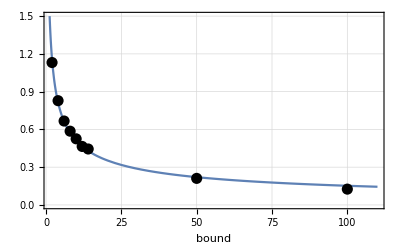
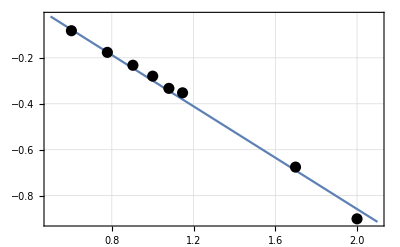

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalTimes=TakeLargestBy[#,#⟦3⟧&,1]⟦1,1⟧&/@dataSets},
With[{points=Table[{ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧,maximalTimes⟦k⟧},{k,Length@maximalTimes}]},
Row@{
Plot[
Evaluate@Fit[points,{1,1/x^(1/2)},x],{x,.5,110},
PlotRange->{{1.5,110},{0,1.5}},ImageSize->400,
Frame->True,Axes->False,GridLines->Automatic,
FrameLabel->{"bound",MaTeX["\\omega\\tau_p",Magnification->2]},
LabelStyle->Directive[Black,FontFamily->"DejaVu Sans",FontSize->18],
Epilog->{PointSize@0.02,Point@points}
],
Plot[
Evaluate@Echo@Fit[Log10@points,{1,x},x],{x,.5,2.1},
PlotRange->All,ImageSize->400,
Frame->True,Axes->False,GridLines->Automatic,
LabelStyle->Directive[Black,FontFamily->"DejaVu Sans",FontSize->18],
Epilog->{PointSize@0.02,Point@Log10@points}
]
}
]]]]
```

0.23456-0.486541 x

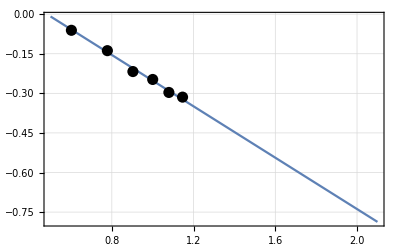

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_100spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalTimes=TakeLargestBy[#,#⟦3⟧&,1]⟦1,1⟧&/@dataSets},
With[{points=Table[{ToExpression@StringTake[#,{-6,-5}]&@datafiles⟦k⟧,maximalTimes⟦k⟧},{k,Length@maximalTimes}]},
Plot[
Evaluate@Echo@Fit[Log10@points,{1,x},x],{x,.5,2.1},
PlotRange->All,ImageSize->400,
Frame->True,Axes->False,GridLines->Automatic,
LabelStyle->Directive[Black,FontFamily->"DejaVu Sans",FontSize->18],
Epilog->{PointSize@0.02,Point@Log10@points}
]
]]]]
```

```mathematica
With[{datafiles=Echo@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalTimes=TakeLargestBy[#,#⟦3⟧&,1]⟦1,1⟧&/@dataSets},
With[{points=Table[{ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧,maximalTimes⟦k⟧},{k,Length@maximalTimes}]},
ExportString[points,"PythonExpression"]//CopyToClipboard
]
]]]
```

```mathematica
Rationalize@0.15
```

3/20

```mathematica
1/6.
```

0.166667

```mathematica
vars={0.0,3.393351800554001,13.573407202216117,30.54016620498612,54.29362880886424,84.83379501385048,122.16066481994471,166.27423822714672,217.1745152354572,274.86149584487544,339.3351800554017,410.59556786703615,488.6426592797784,573.4764542936289,665.0969529085874,763.5041551246538,868.6980609418283,980.678670360111,1099.4459833795017,1225.0};
gs={0.,5.26315789,10.52631579,15.78947368,21.05263158,26.31578947,31.57894737,36.84210526,42.10526316,47.36842105,52.63157895,57.89473684,63.15789474,68.42105263,73.68421053,78.94736842,84.21052632,89.47368421,94.73684211,100.};
```

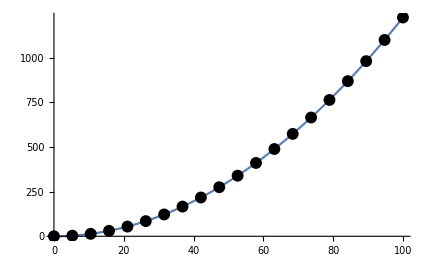

```mathematica
Plot[0.1225 x^2,{x,0,100},
Epilog->{PointSize@0.02,Point@Thread@{gs,vars}}
]
```

```mathematica
Fit[Log10@Rest@Thread@{gs,vars},{1,x},x]
```

-0.911864+2. x

```mathematica
Fit[Rest@Thread@{gs,vars},{1,x^2},x]
```

9.99283×10^-9+0.1225 x^2

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalPoints=TakeLargestBy[#,#⟦3⟧&,1]⟦1,;;2⟧&/@dataSets},
Table[
Join[maximalPoints⟦k⟧,{ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧}],
{k,Length@maximalPoints}
]
]]]
```

{{1.13131,0.737374,2},{0.828283,0.676768,4},{0.666667,0.646465,6},{0.585859,0.636364,8},{0.525253,0.626263,10},{0.464646,0.616162,12},{0.444444,0.616162,14},{0.211055,0.571429,50},{0.125628,0.546366,100}}

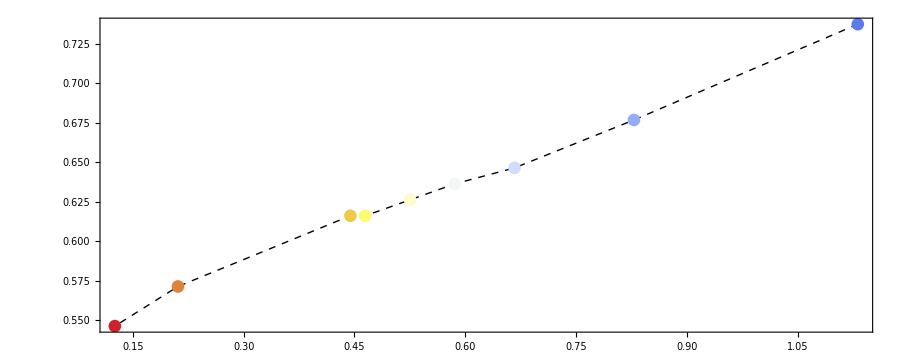

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalPoints=TakeLargestBy[#,#⟦3⟧&,1]⟦1,;;2⟧&/@dataSets},
Graphics[{PointSize@0.01,
{Dashed,Line@maximalPoints},
Table[
{ColorData["TemperatureMap"][k/Length@maximalPoints],
Tooltip[Point@maximalPoints⟦k⟧,ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧]
},{k,Length@maximalPoints}]
},
Frame->True
]
]
]]
```

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalPoints=TakeLargestBy[#,#⟦3⟧&,1]⟦1⟧&/@dataSets},
Graphics3D[{PointSize@0.02,
{Dashed,Line@maximalPoints},
Table[
{ColorData["TemperatureMap"][k/Length@maximalPoints],
Tooltip[Point@maximalPoints⟦k⟧,ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧]
},{k,Length@maximalPoints}]
},
Boxed->True,Axes->True,AxesLabel->{"tf","t1/tf","fid"}
]
]
]]
```

-Graphics3D-

As above, but changing the total number of spins

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_100spins*.csv"}}},
With[{dataSets=Import/@datafiles},
GraphicsRow[Table[
ListContourPlot[
dataSets⟦idx⟧⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",Contours->Append[Range[0,1,0.05],0.99],
PlotRangePadding->None,PlotLabel->StringTake[FileBaseName@datafiles⟦idx⟧,-2],ImagePadding->None,ImageMargins->0,
Frame->True,Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.5,1,1.5,2}}]}
],
{idx,Length@dataSets}
],0,Frame->All,PlotLabel->"100 spins, different boundary constraints",ImageSize->1400]
]]
```

-Graphics-

Use this to plot the different scans above but embedded in a 3D graphics

```mathematica
makeGraphicsComplexPoint3D[obj_GraphicsComplex,thirdCoordinate_]:=obj/.GraphicsComplex[s__,r___]:>GraphicsComplex[Append[#,thirdCoordinate]&/@s,r];
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*.csv"}}},
MapIndexed[
makeGraphicsComplexPoint3D[
ListContourPlot[#1,ColorFunction->"TemperatureMap",Contours->Append[Range[0,1,0.05],0.99]]⟦1⟧,
First@#2
]&,
dataSets
]//Graphics3D
]
```

Contour plot for one of the scans above, but as a ListPlot3D

```mathematica
With[{datafile=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*.csv"}}},
ListPlot3D[
datafile⟦All,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->20
]
]
```

Scan results for bound=50

```mathematica
With[{data=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*bound050*.csv"}}},
ListContourPlot[
data⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->Range[0,0.95,0.05],PlotRange->All,
FrameLabel->{"tf","t1/tf"},PlotRangePadding->None,PerformanceGoal->"Quality"
,Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.2,0.4,0.6,0.8}}]}
]]
```

Scan results for bound=100

```mathematica
With[{data=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*bound100*.csv"}}},
ListContourPlot[
data⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->Range[0,0.9,0.05],PlotRange->All,
FrameLabel->{"tf","t1/tf"},PlotRangePadding->None,PerformanceGoal->"Quality"
,Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.2,0.4,0.6,0.8}}]}
]]
```

```mathematica
With[{datafile=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*bound100*.csv"}}},
ListPlot3D[
datafile⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->20,PlotRange->{All,All,All}
]
]
```